```mathematica
n=30;
p=5;
p'=4;
cv=1-6(p-p')^2/(p p')//Echo[#,"c = "]&;
hv[r_,s_]:=((p r - p' s)^2-(p - p')^2)/(4 p p');
sv[a_,b_]:=2 (2/(p p'))^(1/2)(-1)^(1 + a[[2]]b[[1]]+a[[1]] b[[2]])Sin[π p/p' a[[1]] b[[1]]]Sin[π p'/p a[[2]] b[[2]]] ;
tv[a_,e_:1]:=ⅇ^(2 π ⅈ e(hv[a[[1]],a[[2]]]-cv/24));
ηv[a_]:=(-1)^(a[[1]]+1);
Nv[a_]:=2(-1)^a[[1]] Cos[(π a[[1]])/4];
H=Join[Flatten[Table[{r, s}, {r, 1, Floor[(p'-1)/2]}, {s, 1, p-1}], 1], If[EvenQ[p'], Table[{p'/2, s}, {s, 1, Floor[(p-1)/2]}], {}]];
h = hv @@@ H;
H //Echo[#,"(r,s): "]&;
h //Echo[#,"h = "]&;
s=Outer[sv, H,H,1]//Simplify;
z={
{1,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,2,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{1,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,1},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,2,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,1}
};
t=DiagonalMatrix[tv/@H];
```

c =   7/10

(r,s):   {{1,1},{1,2},{1,3},{1,4},{2,1},{2,2}}

h =   {0,1/10,3/5,3/2,7/16,3/80}

# -------- Modular Bootstrap -----------

```mathematica
i={{{1,1},{1,1},1},{{1,1},{1,1},-1},{{1,2},{1,2},1},{{1,2},{1,2},-1},{{1,3},{1,3},1},{{1,3},{1,3},-1},{{1,4},{1,4},1},{{1,4},{1,4},-1},{{2,2},{2,2},1},{{2,2},{2,2},-1},{{2,4},{2,4},1},{{2,4},{2,4},-1},{{1,1},{1,2},0},{{1,1},{1,3},0},{{1,1},{1,4},0},{{1,1},{2,2},0},{{1,1},{2,4},0},{{1,2},{1,3},0},{{1,2},{1,4},0},{{1,2},{2,2},0},{{1,2},{2,4},0},{{1,3},{1,4},0},{{1,3},{2,2},0},{{1,3},{2,4},0},{{1,4},{2,2},0},{{1,4},{2,4},0},{{2,2},{2,4},0},{{1,1},{1,1},2},{{1,1},{1,1},-2},{{1,2},{1,2},2},{{1,2},{1,2},-2},{{1,3},{1,3},2},{{1,3},{1,3},-2},{{1,4},{1,4},2},{{1,4},{1,4},-2},{{2,2},{2,2},2},{{2,2},{2,2},-2},{{2,4},{2,4},2},{{2,4},{2,4},-2}};
ho[a_]:=(hv@@a[[1]]+hv@@a[[2]]+a[[3]](a[[3]]-1)/2 + {{1,1},{1,1},-1}-a)(1-Abs[a[[3]]]-2)+((hv@@a[[1]])/2 +cv/24 3/2-(a[[3]]-2)/8 + {{1,1},{1,1},-2}-a)Abs[a[[3]]]-2//Simplify;
t=DiagonalMatrix[Exp[2π ⅈ(ho[#]-2 cv/24)]&/@i] // FullSimplify;
(* This is the ugliest way I can write down the s-matrix of this thing *)
sMaker[a_,b_]:= 
(sv[a[[1]],b[[1]]]sv[a[[2]],b[[2]]]+ sv[a[[1]],b[[2]]]sv[a[[2]],b[[1]]])a[[3]]b[[3]]+
sv[a[[1]],b[[1]]]sv[a[[2]],b[[1]]]a[[3]]Abs[b[[3]]]-1+
sv[a[[1]],b[[1]]]sv[a[[1]],b[[2]]]Abs[a[[3]]]-1 b[[3]]+ 
1/2 sv[a[[1]],b[[1]]]^2 Abs[a[[3]]]-1 Abs[b[[3]]]-1+
1/2 a[[3]]sv[a[[1]],b[[1]]]Abs[a[[3]]]-1 Abs[b[[3]]]-2+
1/2 b[[3]]sv[a[[1]],b[[1]]]Abs[a[[3]]]-2 Abs[b[[3]]]-1+
1/8 a[[3]]b[[3]]Total[(sv[a[[1]],#] tv[#]^2 sv[#,b[[1]]])&/@H]Exp[π ⅈ(hv@@(a[[1]]) + hv@@(b[[1]])-cv/12)]Abs[a[[3]]]-2 Abs[b[[3]]]-2;
s=Array[sMaker[i[[#1]],i[[#2]]]&,{Length[i],Length[i]}] // FullSimplify;

(* Here is a T matrix *)
ho[a_]:=(hv@@(a[[1]])+hv@@(a[[2]])+a[[3]](a[[3]]-1)/2 + {{1,1},{1,1},-1}-a)(1-Abs[a[[3]]]-2)+((hv@@(a[[1]]))/2 +cv/24 3/2-(a[[3]]-2)/8 + {{1,1},{1,1},-2}-a)Abs[a[[3]]]-2//Simplify;
t=DiagonalMatrix[Exp[-2π ⅈ(ho[#]-2 cv/24)]&/@i] // FullSimplify;
z=Outer[(KroneckerDelta[#1,#2] + KroneckerDelta[#1[[1]],#2[[1]]]KroneckerDelta[#1[[2]],#2[[2]]]KroneckerDelta[#1[[3]],-#2[[3]]])(1-KroneckerDelta[Abs[#1[[3]]],2])(1-KroneckerDelta[Abs[#2[[3]]],2])&,i,i,1];
```

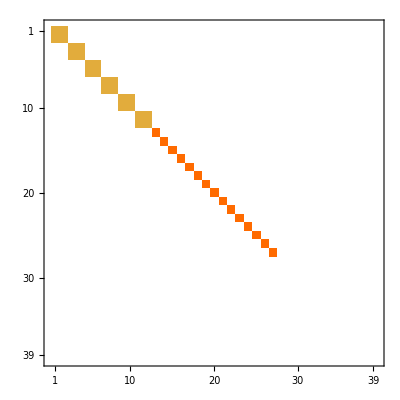

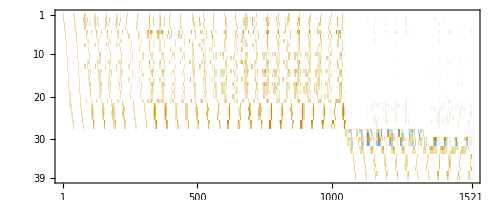

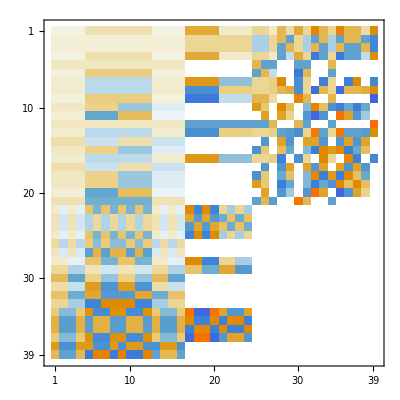

```mathematica
z//MatrixPlot
nz=Position[z, _?(# ≠0 &)];
X=Array[x,Length[nz]];
m=Conjugate[s] . ReplacePart[z,Thread[nz->X]] . s  //Flatten;
A=CoefficientArrays[Thread[m==0],X][[2]]//Simplify//Normal;
a=(A[[#,All]]&/@(Flatten[FirstPosition[#,1]&/@ RowReduce[Transpose[Chop[N[A]]]]]) )//FullSimplify;
Transpose[N[A]]//RowReduce//MatrixPlot
a//MatrixPlot
```

```mathematica
Organize[e_]:=Module[{l,r,L},
l=e[[1]];
r=e[[2]];
L=LCM@@(Level[List@@#,1]&/@Flatten[{l,r}]//Flatten//Denominator);
e[[0]][(l-r)//ExpandAll,0]
];
b=Inverse[N[a]]//Chop;
b=RootApproximant/@b;
y=b.X//Simplify;
m=N[ConjugateTranspose[s] . ReplacePart[z,Thread[nz->y]] . s] ;
eqn=(# ≥ 0 & /@(m//Flatten)) //Expand//Chop//Rationalize//Expand// DeleteDuplicates;
mx=(Min [Cases[eqn, (a_. * #)>= 0 :>a]])^-1&/@X;
m=N[ConjugateTranspose[s] . ReplacePart[z,Thread[nz->Simplify[b.(mx*X)]]] . s] ;
eqn=(# ≥ 0 & /@(m//Flatten)) //Expand//Chop//Rationalize//Expand// DeleteDuplicates;
eqn=Organize/@eqn;
eqn//MatrixForm
```

(x[1]≥0
x[2]≥0
x[3]≥0
x[4]≥0
x[5]≥0
x[6]≥0
x[7]≥0
x[8]≥0
x[9]≥0
x[10]≥0
x[11]≥0
x[12]≥0
x[13]≥0
x[14]≥0
x[15]≥0
x[16]≥0
x[17]≥0
x[18]≥0
x[19]≥0
x[20]≥0
x[21]≥0
x[22]≥0
x[23]≥0
x[24]≥0
x[25]≥0
x[26]≥0
x[27]≥0
x[1]+x[3]+x[8]≥0
x[2]+x[4]+x[13]≥0
x[5]+x[6]+x[21]≥0
x[7]+x[12]≥0
2 x[2]+x[13]≥0
x[14]+x[15]≥0
x[7]+x[9]+x[12]+x[16]≥0
2 x[3]+x[8]≥0
x[10]+x[11]+x[17]+x[18]≥0
x[10]+x[17]≥0
x[12]+x[16]≥0
x[14]+x[15]+x[19]+x[20]≥0
x[14]+x[19]≥0
x[17]+x[18]≥0
2 x[5]+x[21]≥0
x[22]+x[24]≥0
2 x[23]+x[25]≥0
x[22]+2 x[24]≥0
x[23]+x[25]≥0
2 x[26]+x[27]≥0
x[26]+x[27]≥0
x[1]+x[2]+x[3]+x[4]+x[7]+x[8]+x[9]+x[12]+x[13]+x[16]≥0
x[2]+x[3]+x[12]≥0
2 x[5]≥0
x[10]+x[14]+x[17]+x[19]≥0
x[14]+x[17]≥0
2 x[5]+2 x[6]+2 x[21]≥0
x[10]+x[11]+x[14]+x[15]+x[17]+x[18]+x[19]+x[20]≥0
x[14]+x[15]+x[17]+x[18]≥0
2 x[2]+2 x[3]+x[7]+x[8]+2 x[12]+x[13]+x[16]≥0
x[22]+x[23]+x[24]+x[25]≥0
x[22]+2 x[23]+2 x[24]+x[25]≥0
4 x[26]+2 x[27]≥0
2 x[26]+2 x[27]≥0
x[1]+x[4]+x[9]≥0
2 x[6]≥0
x[15]+x[18]≥0
x[11]+x[20]≥0
x[10]+x[19]≥0
x[7]+x[8]+x[13]+x[16]≥0
x[22]+x[25]≥0
x[23]+x[24]≥0
2 x[26]≥0
2 x[27]≥0
2 x[1]+2 x[2]+x[8]≥0
x[7]+x[9]+x[12]≥0
x[8]+x[13]≥0
x[10]+x[11]+x[14]≥0
x[10]+x[15]≥0
2 x[2]+2 x[3]+x[8]+x[13]≥0
x[9]+x[12]+x[16]≥0
x[10]+x[14]+x[15]+x[17]≥0
x[11]+x[14]+x[18]≥0
2 x[3]+2 x[4]+x[13]≥0
x[14]+x[17]+x[18]+x[19]≥0
x[15]+x[17]+x[20]≥0
x[17]+x[19]+x[20]≥0
x[18]+x[19]≥0
2 x[5]+2 x[6]+x[21]≥0
2 x[23]≥0
2 x[22]+2 x[24]≥0
2 x[23]+2 x[25]≥0
2 x[24]≥0
2 x[1]+2 x[3]+x[8]≥0
x[7]+x[16]≥0
x[10]+x[11]+x[17]≥0
x[10]+x[18]≥0
x[7]+2 x[12]+x[16]≥0
2 x[2]+2 x[4]+x[13]≥0
2 x[14]+x[15]+x[19]≥0
x[14]+x[15]+x[20]≥0
x[10]+2 x[17]+x[18]≥0
x[11]+x[17]+x[18]≥0
x[14]+x[19]+x[20]≥0
x[15]+x[19]≥0
2 x[1]+2 x[4]≥0
2 x[2]+2 x[3]≥0
2 x[21]≥0
2 x[25]≥0
2 x[22]≥0
2 x[1]+2 x[5]+x[7]+x[8]+x[9]≥0
x[7]+x[8]+x[21]≥0
2 x[2]+2 x[5]+x[7]+x[12]+x[13]+x[21]≥0
2 x[2]+2 x[6]+x[12]+x[21]≥0
2 x[3]+2 x[5]+x[8]+x[12]+x[16]+x[21]≥0
2 x[3]+2 x[6]+x[12]+x[21]≥0
2 x[4]+2 x[5]+x[9]+x[13]+x[16]≥0
x[13]+x[16]+x[21]≥0
x[11]+x[14]+x[15]+x[17]+x[18]+x[20]≥0
2 x[22]+2 x[23]+2 x[24]+2 x[25]≥0
2 x[23]+2 x[24]≥0
2 x[1]+2 x[6]+x[9]≥0
2 x[2]+2 x[5]+x[12]≥0
x[7]+x[13]+x[21]≥0
2 x[3]+2 x[5]+x[12]≥0
x[8]+x[16]+x[21]≥0
2 x[4]+2 x[6]+x[9]≥0
x[10]+x[15]+x[18]+x[19]≥0
2 x[22]+2 x[25]≥0
2 x[1]+2 x[2]+2 x[3]+2 x[4]+2 x[8]+2 x[13]≥0
4 x[5]+2 x[21]≥0
2 x[22]+4 x[24]≥0
4 x[23]+2 x[25]≥0
2 x[1]+2 x[3]+2 x[5]+2 x[6]+x[7]+2 x[8]+x[9]+x[12]+x[16]+2 x[21]≥0
2 x[3]+2 x[5]+x[7]+x[8]+x[12]+x[21]≥0
2 x[2]+2 x[4]+2 x[5]+2 x[6]+x[7]+x[9]+x[12]+2 x[13]+x[16]+2 x[21]≥0
2 x[2]+2 x[5]+x[12]+x[13]+x[16]+x[21]≥0
x[10]+2 x[14]+x[15]+2 x[17]+x[18]+x[19]≥0
2 x[22]+4 x[23]+4 x[24]+2 x[25]≥0
2 x[1]+2 x[5]+x[8]+x[9]+x[16]≥0
2 x[4]+2 x[5]+x[7]+x[9]+x[13]≥0
x[10]+x[11]+x[14]+x[17]+x[19]+x[20]≥0
2 x[1]+2 x[2]+2 x[3]+2 x[4]+x[7]+x[8]+2 x[9]+2 x[12]+x[13]+x[16]≥0
4 x[26]+4 x[27]≥0
4 x[26]≥0
x[28]≥0
x[29]≥0
x[30]≥0
x[31]≥0
2 x[28]-2 x[29]+2 x[30]-2 x[31]≥0
-2 x[28]+2 x[29]≥0
-2 x[28]+2 x[31]≥0
2 x[32]≥0
2 x[33]≥0
-2 x[29]+2 x[30]≥0
2 x[32]+2 x[33]≥0
2 x[30]-2 x[31]≥0
x[34]≥0
x[35]≥0
x[36]≥0
x[37]≥0
x[38]≥0
x[39]≥0
x[28]-x[29]+x[30]-x[31]≥0
x[28]-2 x[29]+2 x[30]-x[31]≥0
2 x[30]-x[31]≥0
x[30]-x[31]≥0
2 x[29]≥0
-2 x[28]+4 x[29]≥0
4 x[32]+2 x[33]≥0
2 x[30]≥0
x[34]+x[36]≥0
x[35]+x[37]≥0
x[38]+x[39]≥0
-x[28]+x[29]≥0
-x[28]+2 x[29]≥0
2 x[28]-4 x[29]+4 x[30]-2 x[31]≥0
-x[28]+x[31]≥0
-x[29]+x[30]≥0
2 x[28]≥0
x[32]≥0
2 x[32]+x[33]≥0
4 x[30]-2 x[31]≥0
4 x[32]+4 x[33]≥0
x[34]+x[35]+x[36]+x[37]≥0
x[35]+x[36]≥0
x[33]≥0
x[32]+x[33]≥0
2 x[31]≥0
4 x[32]≥0
x[34]+x[37]≥0)

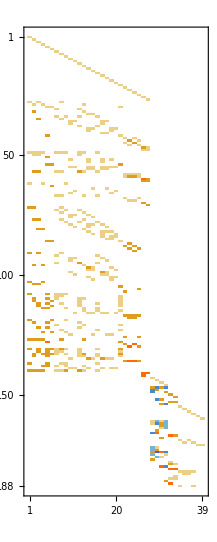

```mathematica
B=Table[Coefficient[eqn[[i]][[1]],X],{i,Length[eqn]}];
B//MatrixPlot
```

```mathematica
<<math4ti2`
basis =zsolve[#>=0&/@Flatten[B.X]][[2]];
basis//MatrixForm
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
d=b. (mx*#) &/@basis //FullSimplify;
d=Sort[d,#1[[1]] <= #2[[1]]&];
(*d//Transpose//MatrixForm*)
dd=FullSimplify[d, TransformationFunctions -> {Automatic, # /. Sqrt[5] -> 2GoldenRatio - 1 &}];
dd=FullSimplify[dd, TransformationFunctions -> {#/. 1+GoldenRatio ->GoldenRatio^2&,Automatic}];
dd=FullSimplify[dd,TransformationFunctions->{# /. Sqrt[5+Sqrt[5]]->Sqrt[2(1 + GoldenRatio^2)]&,# /.Sqrt[5+2Sqrt[5]]->Sqrt[(GoldenRatio+2)]*GoldenRatio&,#/.Sqrt[10+4Sqrt[5]]->Sqrt[2(GoldenRatio+2)]*GoldenRatio&,#/. 2-GoldenRatio->1/(GoldenRatio)^2&}];
dd/.GoldenRatio->φ //Transpose//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | φ | φ | φ | φ | φ | φ | 2 | √2 φ | √2 φ | √2 φ | √2 φ | √2 φ | φ^2 | φ^2 | φ^2 | 2 φ | √2 φ^2 | √2 φ^2 | 2 √(2+φ) | 2 √(2+φ) | 2 √(2+φ) | 2 √(2+φ) | 2 φ^2 | 2 √2 √(2+φ) | 2 √2 √(2+φ) | 2 φ √(2+φ) | 2 φ √(2+φ) | 2 φ √(2+φ) | 2 φ √(2+φ) | 2 √2 φ √(2+φ) | 2 √2 φ √(2+φ)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | φ | φ | φ | φ | -φ | -φ | 2 | √2 φ | √2 φ | √2 φ | √2 φ | -√2 φ | φ^2 | φ^2 | φ^2 | 2 φ | √2 φ^2 | √2 φ^2 | -2 √(2+φ) | -2 √(2+φ) | 2 √(2+φ) | 2 √(2+φ) | 2 φ^2 | -2 √2 √(2+φ) | 2 √2 √(2+φ) | -2 φ √(2+φ) | -2 φ √(2+φ) | 2 φ √(2+φ) | 2 φ √(2+φ) | -2 √2 φ √(2+φ) | 2 √2 φ √(2+φ)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | φ | φ | φ | φ | -φ | -φ | 2 | √2 φ | √2 φ | √2 φ | √2 φ | -√2 φ | φ^2 | φ^2 | φ^2 | 2 φ | √2 φ^2 | √2 φ^2 | 2 √(2+φ) | 2 √(2+φ) | -2 √(2+φ) | -2 √(2+φ) | 2 φ^2 | 2 √2 √(2+φ) | -2 √2 √(2+φ) | 2 φ √(2+φ) | 2 φ √(2+φ) | -2 φ √(2+φ) | -2 φ √(2+φ) | 2 √2 φ √(2+φ) | -2 √2 φ √(2+φ)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | φ | φ | φ | φ | φ | φ | 2 | √2 φ | √2 φ | √2 φ | √2 φ | √2 φ | φ^2 | φ^2 | φ^2 | 2 φ | √2 φ^2 | √2 φ^2 | -2 √(2+φ) | -2 √(2+φ) | -2 √(2+φ) | -2 √(2+φ) | 2 φ^2 | -2 √2 √(2+φ) | -2 √2 √(2+φ) | -2 φ √(2+φ) | -2 φ √(2+φ) | -2 φ √(2+φ) | -2 φ √(2+φ) | -2 √2 φ √(2+φ) | -2 √2 φ √(2+φ)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1-φ | 1-φ | 1-φ | 1-φ | 1-φ | 1-φ | 2 | √(4-2 φ) | √(4-2 φ) | √(4-2 φ) | √(4-2 φ) | √(4-2 φ) | 1/φ^2 | 1/φ^2 | 1/φ^2 | 2-2 φ | √2 (-2+φ) | √2 (-2+φ) | 2 √(3-φ) | 2 √(3-φ) | 2 √(3-φ) | 2 √(3-φ) | 4-2 φ | -2 √(6-2 φ) | -2 √(6-2 φ) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1-φ | 1-φ | 1-φ | 1-φ | -1+φ | -1+φ | 2 | √(4-2 φ) | √(4-2 φ) | √(4-2 φ) | √(4-2 φ) | -√2 (-1+φ) | 1/φ^2 | 1/φ^2 | 1/φ^2 | 2-2 φ | √2 (-2+φ) | √2 (-2+φ) | -2 √(3-φ) | -2 √(3-φ) | 2 √(3-φ) | 2 √(3-φ) | 4-2 φ | 2 √(6-2 φ) | -2 √(6-2 φ) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1-φ | 1-φ | 1-φ | 1-φ | -1+φ | -1+φ | 2 | √(4-2 φ) | √(4-2 φ) | √(4-2 φ) | √(4-2 φ) | -√2 (-1+φ) | 1/φ^2 | 1/φ^2 | 1/φ^2 | 2-2 φ | √2 (-2+φ) | √2 (-2+φ) | 2 √(3-φ) | 2 √(3-φ) | -2 √(3-φ) | -2 √(3-φ) | 4-2 φ | -2 √(6-2 φ) | 2 √(6-2 φ) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1-φ | 1-φ | 1-φ | 1-φ | 1-φ | 1-φ | 2 | √(4-2 φ) | √(4-2 φ) | √(4-2 φ) | √(4-2 φ) | √(4-2 φ) | 1/φ^2 | 1/φ^2 | 1/φ^2 | 2-2 φ | √2 (-2+φ) | √2 (-2+φ) | -2 √(3-φ) | -2 √(3-φ) | -2 √(3-φ) | -2 √(3-φ) | 4-2 φ | 2 √(6-2 φ) | 2 √(6-2 φ) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1-φ | 1-φ | 1-φ | 1-φ | 1-φ | 1-φ | 2 | -√2 (-1+φ) | -√2 (-1+φ) | -√2 (-1+φ) | -√2 (-1+φ) | -√2 (-1+φ) | 1/φ^2 | 1/φ^2 | 1/φ^2 | 2-2 φ | (4-2 φ)/(√2) | (4-2 φ)/(√2) | 2 √(3-φ) | 2 √(3-φ) | 2 √(2+φ)+ | 2 √(2+φ)+ | 4-2 φ | 2 √(6-2 φ) | 2 √(6-2 φ) | -2 √(5-2 √5) | -2 √(5-2 √5) |  |  | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1-φ | 1-φ | 1-φ | 1-φ | -1+φ | -1+φ | 2 | -√2 (-1+φ) | -√2 (-1+φ) | -√2 (-1+φ) | -√2 (-1+φ) | √(4-2 φ) | 1/φ^2 | 1/φ^2 | 1/φ^2 | 2-2 φ | (4-2 φ)/(√2) | (4-2 φ)/(√2) | -2 √(3-φ) | -2 √(3-φ) | 2 √(3-φ) | 2 √(3-φ) | 4-2 φ | -2 √(6-2 φ) | 2 √(6-2 φ) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1-φ | 1-φ | 1-φ | 1-φ | -1+φ | -1+φ | 2 | -√2 (-1+φ) | -√2 (-1+φ) | -√2 (-1+φ) | -√2 (-1+φ) | √(4-2 φ) | 1/φ^2 | 1/φ^2 | 1/φ^2 | 2-2 φ | (4-2 φ)/(√2) | (4-2 φ)/(√2) | 2 √(3-φ) | 2 √(3-φ) | -2 √(3-φ) | -2 √(3-φ) | 4-2 φ | 2 √(6-2 φ) | -2 √(6-2 φ) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1-φ | 1-φ | 1-φ | 1-φ | 1-φ | 1-φ | 2 | -√2 (-1+φ) | -√2 (-1+φ) | -√2 (-1+φ) | -√2 (-1+φ) | -√2 (-1+φ) | 1/φ^2 | 1/φ^2 | 1/φ^2 | 2-2 φ | (4-2 φ)/(√2) | (4-2 φ)/(√2) | -2 √(3-φ) | -2 √(3-φ) | -2 √(3-φ) | -2 √(3-φ) | 4-2 φ | -2 √(6-2 φ) | -2 √(6-2 φ) |  | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | φ | φ | φ | φ | φ | φ | 2 | -√2 φ | -√2 φ | -√2 φ | -√2 φ | -√2 φ | φ^2 | φ^2 | φ^2 | 2 φ | -√2 φ^2 | -√2 φ^2 | 2 √(2+φ) | 2 √(2+φ) | 2 √(2+φ) | 2 √(2+φ) | 2 φ^2 | -2 √2 √(2+φ) | -2 √2 √(2+φ) | 2 φ √(2+φ) | 2 φ √(2+φ) | 2 φ √(2+φ) | 2 φ √(2+φ) | -2 √2 φ √(2+φ) | -2 √2 φ √(2+φ)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | φ | φ | φ | φ | -φ | -φ | 2 | -√2 φ | -√2 φ | -√2 φ | -√2 φ | √2 φ | φ^2 | φ^2 | φ^2 | 2 φ | -√2 φ^2 | -√2 φ^2 | -2 √(2+φ) | -2 √(2+φ) | 2 √(2+φ) | 2 √(2+φ) | 2 φ^2 | 2 √2 √(2+φ) | -2 √2 √(2+φ) | -2 φ √(2+φ) | -2 φ √(2+φ) | 2 φ √(2+φ) | 2 φ √(2+φ) | 2 √2 φ √(2+φ) | -2 √2 φ √(2+φ)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | φ | φ | φ | φ | -φ | -φ | 2 | -√2 φ | -√2 φ | -√2 φ | -√2 φ | √2 φ | φ^2 | φ^2 | φ^2 | 2 φ | -√2 φ^2 | -√2 φ^2 | 2 √(2+φ) | 2 √(2+φ) | -2 √(2+φ) | -2 √(2+φ) | 2 φ^2 | -2 √2 √(2+φ) | 2 √2 √(2+φ) | 2 φ √(2+φ) | 2 φ √(2+φ) | -2 φ √(2+φ) | -2 φ √(2+φ) | -2 √2 φ √(2+φ) | 2 √2 φ √(2+φ)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | φ | φ | φ | φ | φ | φ | 2 | -√2 φ | -√2 φ | -√2 φ | -√2 φ | -√2 φ | φ^2 | φ^2 | φ^2 | 2 φ | -√2 φ^2 | -√2 φ^2 | -2 √(2+φ) | -2 √(2+φ) | -2 √(2+φ) | -2 √(2+φ) | 2 φ^2 | 2 √2 √(2+φ) | 2 √2 √(2+φ) | -2 φ √(2+φ) | -2 φ √(2+φ) | -2 φ √(2+φ) | -2 φ √(2+φ) | 2 √2 φ √(2+φ) | 2 √2 φ √(2+φ)
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | -1+φ | 1-φ | 1-φ | -1+φ | -1+φ | 1-φ | 0 | 0 | 0 | 0 | 0 | 0 | 1/φ^2 | 1/φ^2 | -2+φ | 0 | 0 | 0 | √(6-2 φ) | -√(6-2 φ) | √(6-2 φ) | -√(6-2 φ) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | -1+φ | 1-φ | 1-φ | -1+φ | 1-φ | -1+φ | 0 | 0 | 0 | 0 | 0 | 0 | 1/φ^2 | 1/φ^2 | -2+φ | 0 | 0 | 0 | -√(6-2 φ) | √(6-2 φ) | √(6-2 φ) | -√(6-2 φ) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | -1+φ | 1-φ | 1-φ | -1+φ | 1-φ | -1+φ | 0 | 0 | 0 | 0 | 0 | 0 | 1/φ^2 | 1/φ^2 | -2+φ | 0 | 0 | 0 | √(6-2 φ) | -√(6-2 φ) | -√(6-2 φ) | √(6-2 φ) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | -1+φ | 1-φ | 1-φ | -1+φ | -1+φ | 1-φ | 0 | 0 | 0 | 0 | 0 | 0 | 1/φ^2 | 1/φ^2 | -2+φ | 0 | 0 | 0 | -√(6-2 φ) | √(6-2 φ) | -√(6-2 φ) | √(6-2 φ) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | -φ | φ | φ | -φ | -φ | φ | 0 | 0 | 0 | 0 | 0 | 0 | φ^2 | φ^2 | -1-φ | 0 | 0 | 0 | √2 √(2+φ) | -√2 √(2+φ) | √2 √(2+φ) | -√2 √(2+φ) | 0 | 0 | 0 | -√2 φ √(2+φ) | √2 φ √(2+φ) | √2 φ √(2+φ) | -√2 φ √(2+φ) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | -φ | φ | φ | -φ | φ | -φ | 0 | 0 | 0 | 0 | 0 | 0 | φ^2 | φ^2 | -1-φ | 0 | 0 | 0 | -√2 √(2+φ) | √2 √(2+φ) | √2 √(2+φ) | -√2 √(2+φ) | 0 | 0 | 0 | √2 φ √(2+φ) | -√2 φ √(2+φ) | √2 φ √(2+φ) | -√2 φ √(2+φ) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | -φ | φ | φ | -φ | φ | -φ | 0 | 0 | 0 | 0 | 0 | 0 | φ^2 | φ^2 | -1-φ | 0 | 0 | 0 | √2 √(2+φ) | -√2 √(2+φ) | -√2 √(2+φ) | √2 √(2+φ) | 0 | 0 | 0 | -√2 φ √(2+φ) | √2 φ √(2+φ) | -√2 φ √(2+φ) | √2 φ √(2+φ) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | -φ | φ | φ | -φ | -φ | φ | 0 | 0 | 0 | 0 | 0 | 0 | φ^2 | φ^2 | -1-φ | 0 | 0 | 0 | -√2 √(2+φ) | √2 √(2+φ) | -√2 √(2+φ) | √2 √(2+φ) | 0 | 0 | 0 | √2 φ √(2+φ) | -√2 φ √(2+φ) | -√2 φ √(2+φ) | √2 φ √(2+φ) | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | √10 | -√10 | -√10 | √10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 2 √2 | 2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | √2 | √2 | √2 | √2 | 0 | -2 | -2 | -2 | 2 | -2 √2 | -2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 2 φ | 2 φ | 2 φ | 2 φ | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 2 φ^2 | 2 φ^2 | 2 φ^2 | -4 φ | 0 | 0 | 0 | 0 | 0 | 0 | -4 φ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | √5 | 1 | -1 | 1-2 φ | 0 | 0 | 0 | √2 φ | √(4-2 φ) | -√2 (-1+φ) | -√2 φ | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 2 φ | -2 φ | 0 | 0 | 0 | 0 | √2 φ | -√2 φ | √2 φ | -√2 φ | 0 | -2 φ^2 | 2 φ^2 | 0 | 0 | -√2 φ^2 | √2 φ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 2-2 φ | 2-2 φ | 2-2 φ | 2-2 φ | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 4-2 φ | 4-2 φ | 4-2 φ | 4 (-1+φ) | 0 | 0 | 0 | 0 | 0 | 0 | 4 (-2+φ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | -2 √2 | -2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | -√2 | -√2 | -√2 | -√2 | 0 | -2 | -2 | -2 | 2 | 2 √2 | 2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 2-2 φ | 2 (-1+φ) | 0 | 0 | 0 | 0 | √(4-2 φ) | -√2 (-1+φ) | √(4-2 φ) | -√2 (-1+φ) | 0 | 2 (-2+φ) | 4-2 φ | 0 | 0 | (4-2 φ)/(√2) | √2 (-2+φ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 1-2 φ | 1 | -1 | √5 | 0 | 0 | 0 | √(4-2 φ) | √2 φ | -√2 φ | -√2 (-1+φ) | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | -√10 | √10 | √10 | -√10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 2-2 φ | 2 (-1+φ) | 0 | 0 | 0 | 0 | -√2 (-1+φ) | √(4-2 φ) | -√2 (-1+φ) | √(4-2 φ) | 0 | 2 (-2+φ) | 4-2 φ | 0 | 0 | √2 (-2+φ) | (4-2 φ)/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 1-2 φ | 1 | -1 | √5 | 0 | 0 | 0 | -√2 (-1+φ) | -√2 φ | √2 φ | √(4-2 φ) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | √5 | 1 | -1 | 1-2 φ | 0 | 0 | 0 | -√2 φ | -√2 (-1+φ) | √(4-2 φ) | √2 φ | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 2 φ | -2 φ | 0 | 0 | 0 | 0 | -√2 φ | √2 φ | -√2 φ | √2 φ | 0 | -2 φ^2 | 2 φ^2 | 0 | 0 | √2 φ^2 | -√2 φ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | -2 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

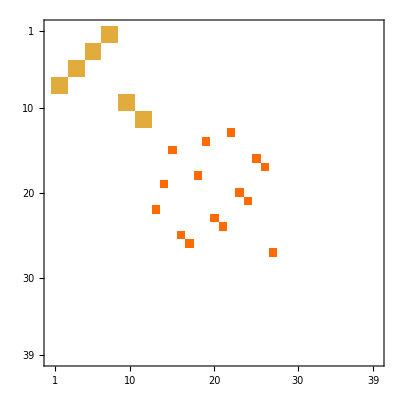

-Graphics-

```mathematica
ti=s.t.s.t.s // N;
P={t,ti};
MM= ConjugateTranspose[s].ReplacePart[z,Thread[nz->d[[2]]]].s//N//Chop//RootApproximant;
out=Chop[N[ConjugateTranspose[#].MM.#]]&/@P;
(*MM//MatrixForm*)
MM//MatrixPlot
Show[GraphicsRow[MapThread[Legended[#1,Placed[#2,Below]]&,{{MatrixPlot[out[[1]],ImageSize->Full],MatrixPlot[out[[2]],ImageSize->Full]},{"1", "2"}}],Spacings->0],PlotLabel->HoldForm["Difference"],LabelStyle->{GrayLevel[0]},ImageSize->Large]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | -2 | 0 | 0 | -2 | 2 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0)

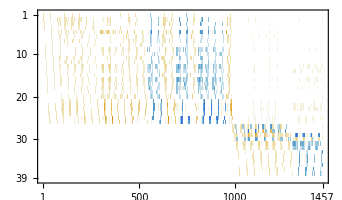

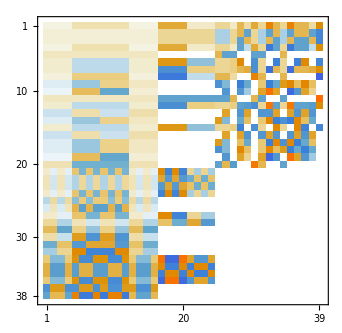

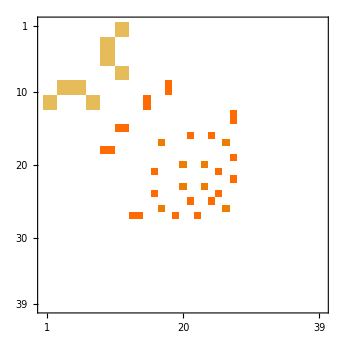

```mathematica
Clear[y];
Nz=Position[MM, _?(# ≠0 &)];
zeroes=Position[ConjugateTranspose[s].ReplacePart[z,Thread[nz->d[[15]]]].s//N//Chop,_?(# ==0 &)];
Y=Array[y,Length[Nz]];
my=Extract[Conjugate[s] . ReplacePart[MM,Thread[Nz->Y]] . s,zeroes];
Ay=CoefficientArrays[Thread[my==0],Y][[2]]//Simplify//Normal;
ay=(Ay[[#,All]]&/@(DeleteMissing[Flatten[FirstPosition[#,1]&/@ RowReduce[Transpose[Chop[N[Ay]]]]]]) )//FullSimplify;
(*LinearSolve[ay//N,0&/@Y]*)
act=RootApproximant/@(NullSpace[ay//N]//Chop);
act/Min[Select[Abs[act]//Flatten, #!=0&]] //MatrixForm
Transpose[N[Ay]]//RowReduce//MatrixPlot
ay//MatrixPlot
ConjugateTranspose[s].ReplacePart[z,Thread[nz->d[[15]]]].s//N//Chop//MatrixPlot
(*ReplacePart[MM,Thread[Nz->Y]]*)
```

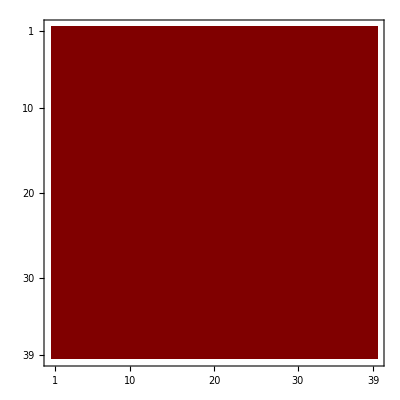

```mathematica
Q =Conjugate[s] . ReplacePart[MM,Thread[Nz->Y]] . s//N//Chop//ExpandAll;
Q//MatrixPlot
(*pos=Cases[Position[Q,Except[0],{2}],{_?Positive,_?Positive}];
ReplacePart[Q,Thread[pos->1]]//MatrixPlot*)
```

```mathematica
Dimensions[Q]
```

{39,39}

```mathematica
k=24;
DD=(d[[4]]d[[6]])[[;;k]]//N;
M=Transpose[d][[;;k]]//N;
nn=Length[M[[1]]];
solution={ConstantArray[0,nn]};
```

```mathematica
solution=Append[solution,LinearProgramming[Total@solution,M,Transpose[{DD,ConstantArray[0,Length[DD]]}],ConstantArray[{0,Infinity},nn],Integers]];
solution//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

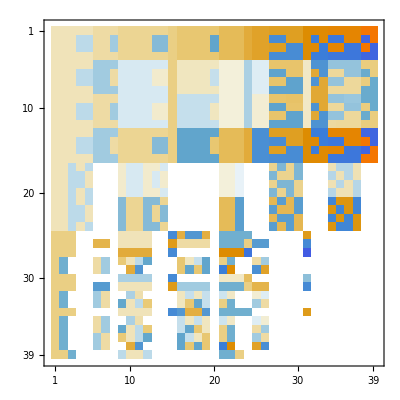

```mathematica
Transpose[d][[;;k]]//MatrixPlot
```